```mathematica
ClearAll["Global`*"]
```

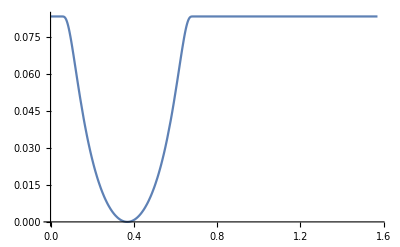

{{0,1/12},{1/8,0.0595588},{1/4,0.0117995},{3/8,0.0000270889},{1/2,0.0144529},{5/8,0.0660632},{3/4,1/12},{7/8,1/12},{1,1/12}}

```mathematica
(*testData={{10,10},{10,20},{10,25},{10,27},{10,28},{9,26},{8,25},{5,20},{3,1}};*)
l=10;(*This is to scale the x axis*)
a=14;
b=0;
bbf=1/12;
tavg=Pi/4;
tdev=Pi/8;
bf[t_]:=Piecewise[{{bbf*(1-Exp[1-1/(1-(t-tavg)^2/(tdev)^2)]),tavg-tdev<t<tavg+tdev}},bbf]
h1[x_]:=bf[(x+tavg-1/2)*1.2]
(*h1[x_]:=((l*x)^4/4-a/3*(l*x)^3+(b+1/4)*a^2/2*(l*x)^2)/((l*1)^4/4-a/3*(l*1)^3+(b+1/4)*a^2/2*(l*1)^2)+1 *)
Plot[h1[x],{x,0,Pi/2}]
testData=Table[{i/8,h1[i/8]},{i,0,8}]
```

```mathematica
parametrizeCurve[pts_/;MatrixQ[pts,NumericQ],a:(_?NumericQ):1/2]:=FoldList[Plus,0,Normalize[(Norm/@Differences[pts])^a,Total]]
(*This creates a list of the parameter points using the centripetal parameterization method.
1. /; is a Conditional pattern test 
pattern/;test 
is a pattern iif test is true
eg:-
{6,-7,3,2,-1,-2}/. x_/;x<0->w
replaces all the negative values with w.

2.MatrixQ[expr,test]
gives True only if test yields True when applied to each of the matrix elements in expr.
3. p?test
is a pattern object that stands for any expression that matches p,and on which the application of test gives True.
*)
tvals=parametrizeCurve[testData];
(*This is another way to test the way in which they generate tvals
Tot=0;
d=Range[Nx];
For[i=1,i<=Nx,i++,Tot=Tot+Sqrt[EuclideanDistance[testData[[i]],testData[[i+1]]]];d[[i]]=Tot]
Total[(d/Tot-tvals[[2;;Nx+1]])^2]//N*)
```

```mathematica
m=3;(*degree of the B-spline*)(*knots for interpolating B-spline*)
ConstantArray[0,m+1];
ArrayPad[tvals,-1];(*gets rid of one term on either side*)
MovingAverage[ArrayPad[tvals,-1],m];(*Moving average is when you compute the average of m consecutive points.*)
ConstantArray[1,m+1];
knots=Join[ConstantArray[0,m+1],MovingAverage[ArrayPad[tvals,-1],m],ConstantArray[1,m+1]];
(*basis function matrix*)
bas=Table[BSplineBasis[{m,knots},j-1,tvals[[i]]]//N,{i,Length[testData]},{j,Length[testData]}];
ctrlpts=LinearSolve[bas,testData]
```

{{0.,0.0833333},{0.0871473,0.0923631},{0.204854,0.00443151},{0.375059,-0.00162593},{0.503041,0.00375928},{0.622011,0.0761486},{0.791486,0.0880421},{0.916316,0.0809996},{1.,0.0833333}}

```mathematica
{Graphics[{{ColorData[1,1],BSplineCurve[ctrlpts,SplineDegree->m,SplineKnots->knots]},{Directive[Green,AbsolutePointSize[6]],Point[testData]}},Frame->True],ParametricPlot[BSplineFunction[ctrlpts,SplineDegree->m,SplineKnots->knots][t]//Evaluate,{t,0,1},Axes->None,Epilog->{Directive[Green,AbsolutePointSize[6]],Point[testData]},Frame->True]}//GraphicsRow
```

-Graphics-

```mathematica
Ctrlx:={{0.,1.},{0.10639159293510557,1.0375550337803687},{0.2126969952069839,1.258380854208646},{0.363009599063995,1.5152219072171749},{0.48433884300668323,1.6597080512483517},{0.6208684308346045,1.7139951801955178},{0.8136003777559151,1.6889027015898332},{0.9585286885149434,1.7939757930941866},{1.,2.}}
Ctrly:={{0.,1.},{0.08595020040033262,0.9996966275167547},{0.21627343053071482,1.0349898983254209},{0.38116492140183156,1.14005162514257},{0.5064509131756854,1.251282139199766},{0.6313085146911201,1.393361347095262},{0.8016121884251431,1.6296426634436192},{0.921578440298442,1.8433428227210027},{1.,2.}}
Ctrl=Table[{Ctrlx[[i]][[1]],Ctrly[[j]][[1]],Ctrlx[[i]][[2]]*Ctrly[[j]][[2]]},{i,1,Length[Ctrlx]},{j,1,Length[Ctrly]}];
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,Ctrl],Gray,Line[Ctrl],Line[Transpose[Ctrl]]}],Graphics3D[BSplineSurface[Ctrl]],Plot3D[(((l*x)^4/4-a/3*(l*x)^3+(b+1/4)*a^2/2*(l*x)^2)/((l*1)^4/4-a/3*(l*1)^3+(b+1/4)*a^2/2*(l*1)^2)+1)*(1+y^2),{x,0,1},{y,0,1}]]
```

-Graphics3D-